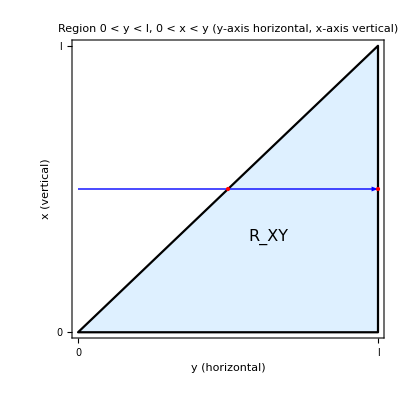

```mathematica
(*Parameters*)l=5;
x0=2.5;

Show[RegionPlot[0<y<l&&0<x<y,{y,0,l},{x,0,l},PlotStyle->LightBlue,BoundaryStyle->Black,Frame->True,FrameLabel->{"y (horizontal)","x (vertical)"},FrameTicks->{{{{0,"0"},{l,"l"}},None},{{{0,"0"},{l,"l"}},None}},AspectRatio->1],Graphics[{Blue,Thick,Arrow[{{0,x0},{l,x0}}],(*blue horizontal arrow*)Red,PointSize[Large],Point[{x0,x0}],(*intersection with y=x*)Point[{l,x0}],(*intersection with y=l*)Black,FontSize->16,Text[Style["R_XY",Italic,Black,16],{l/3+1.5,l/3}]  (*label region*)}],PlotLabel->"Region  0 < y < l,  0 < x < y  (y-axis horizontal, x-axis vertical)"]
```